Triple pendulum

## Lagrangian (exact calculation)

Kinetic energy

```mathematica
Clear["Global`*"]
```

```mathematica
T1 = 3m l^2 Subscript[ϕ̇, 1]^2;
T2 = m l^2 (Subscript[ϕ̇, 1]^2 + Subscript[ϕ̇, 2]^2 + 2 Subscript[ϕ̇, 1] Subscript[ϕ̇, 2] Cos[Subscript[ϕ, 1] - Subscript[ϕ, 2]]);
T3 = 1/2 m l^2 (Subscript[ϕ̇, 1]^2 + Subscript[ϕ̇, 2]^2 + Subscript[ϕ̇, 3]^2+ 2 Subscript[ϕ̇, 1] Subscript[ϕ̇, 2] Cos[Subscript[ϕ, 1] - Subscript[ϕ, 2]] + 2 Subscript[ϕ̇, 1] Subscript[ϕ̇, 3] Cos[Subscript[ϕ, 1] - Subscript[ϕ, 3]] + 2 Subscript[ϕ̇, 2] Subscript[ϕ̇, 3] Cos[Subscript[ϕ, 2] - Subscript[ϕ, 3]]);
T = T1 + T2 + T3;
T // Simplify
```

1/2 l^2 m (9 (ϕ̇)_1^2+3 (ϕ̇)_2^2+2 Cos[ϕ_2-ϕ_3] (ϕ̇)_2 (ϕ̇)_3+(ϕ̇)_3^2+2 (ϕ̇)_1 (3 Cos[ϕ_1-ϕ_2] (ϕ̇)_2+Cos[ϕ_1-ϕ_3] (ϕ̇)_3))

Potential Energy

```mathematica
U1 = -6m g l Cos[Subscript[ϕ, 1]];
U2 = -2m g l (Cos[Subscript[ϕ, 1]] + Cos[Subscript[ϕ, 2]]);
U3 = -m g l (Cos[Subscript[ϕ, 1]] + Cos[Subscript[ϕ, 2]] + Cos[Subscript[ϕ, 3]]);
U = U1 + U2 + U3;
U // Simplify
```

-g l m (9 Cos[ϕ_1]+3 Cos[ϕ_2]+Cos[ϕ_3])

Lagrangian

```mathematica
L = Simplify[T] - Simplify[U]
```

g l m (9 Cos[ϕ_1]+3 Cos[ϕ_2]+Cos[ϕ_3])+1/2 l^2 m (9 (ϕ̇)_1^2+3 (ϕ̇)_2^2+2 Cos[ϕ_2-ϕ_3] (ϕ̇)_2 (ϕ̇)_3+(ϕ̇)_3^2+2 (ϕ̇)_1 (3 Cos[ϕ_1-ϕ_2] (ϕ̇)_2+Cos[ϕ_1-ϕ_3] (ϕ̇)_3))

## Small angle approximation

Kinetic energy

```mathematica
T1Approx = 3m l^2 Subscript[ϕ̇, 1]^2;
```

```mathematica
T2Approx =  m l^2(Subscript[ϕ̇, 1]^2 +Subscript[ϕ̇, 2]^2 +2 Subscript[ϕ̇, 1] Subscript[ϕ̇, 2]);
```

```mathematica
T3Approx =  1/2 m l^2(Subscript[ϕ̇, 1]^2 +Subscript[ϕ̇, 2]^2 + Subscript[ϕ̇, 3]^2+ 2 Subscript[ϕ̇, 1] Subscript[ϕ̇, 2] + 2 Subscript[ϕ̇, 1] Subscript[ϕ̇, 3] + 2 Subscript[ϕ̇, 2] Subscript[ϕ̇, 3]);
```

```mathematica
TApprox = T1Approx+ T2Approx + T3Approx;
TApprox // Simplify
```

1/2 l^2 m (9 (ϕ̇)_1^2+3 (ϕ̇)_2^2+2 (ϕ̇)_2 (ϕ̇)_3+(ϕ̇)_3^2+2 (ϕ̇)_1 (3 (ϕ̇)_2+(ϕ̇)_3))

Potential energy

```mathematica
U1Approx = 3m g l Subscript[ϕ, 1]^2;
```

```mathematica
U2Approx = m g l(Subscript[ϕ, 1]^2 + Subscript[ϕ, 2]^2);
```

```mathematica
U3Approx = 1/2 m g l(Subscript[ϕ, 1]^2 + Subscript[ϕ, 2]^2 + Subscript[ϕ, 3]^2 );
```

```mathematica
UApprox = U1Approx + U2Approx + U3Approx;
UApprox // Simplify
```

1/2 g l m (9 ϕ_1^2+3 ϕ_2^2+ϕ_3^2)

“Mass” and “spring-constant” matrices

```mathematica
M = m l^2{{9, 3, 1}, {3, 3, 1}, {1, 1, 1}};
```

```mathematica
M // MatrixForm
```

(9 l^2 m | 3 l^2 m | l^2 m
3 l^2 m | 3 l^2 m | l^2 m
l^2 m | l^2 m | l^2 m)

```mathematica
K = m g l{{9, 0, 0}, {0, 3, 0}, {0, 0, 1}};
K // MatrixForm
```

(9 g l m | 0 | 0
0 | 3 g l m | 0
0 | 0 | g l m)

Characteristic equation

```mathematica
d = Det[(K - Ω M)]
```

27 g^3 l^3 m^3-81 g^2 l^4 m^3 Ω+60 g l^5 m^3 Ω^2-12 l^6 m^3 Ω^3

```mathematica
s = Solve[d == 0, Ω]
```

{{Ω→g/(2 l)},{Ω→(3 g)/(2 l)},{Ω→(3 g)/l}}

Equations of motion

```mathematica
NullSpace[(K - Ω M) /.  s[[1]]]
```

{{1/3,2/3,1}}

```mathematica
NullSpace[(K - Ω M) /. s[[2]]]
```

{{-1/3,0,1}}

```mathematica
NullSpace[(K - Ω M) /. s[[3]]]
```

{{1/3,-1,1}}

```mathematica
a1 = NullSpace[(K - Ω M) /.  s[[1]]][[1]];
a2 = NullSpace[(K - Ω M) /. s[[2]]][[1]];
a3 = NullSpace[(K - Ω M) /. s[[3]]][[1]];
```

```mathematica
Subscript[ω, 1] = Sqrt[Ω] /. s[[1]];
Subscript[ω, 2] = Sqrt[Ω] /. s[[2]];
Subscript[ω, 3] = Sqrt[Ω] /. s[[3]];
```

```mathematica
Subscript[ϕ, 1][t_, A_, δ_] = A a1 Cos[Subscript[ω, 1] t - δ];
```

```mathematica
legendToPlot = {"ϕ_1(t)", "ϕ_2(t)", "ϕ_3(t)"};
tMax = 10;
```

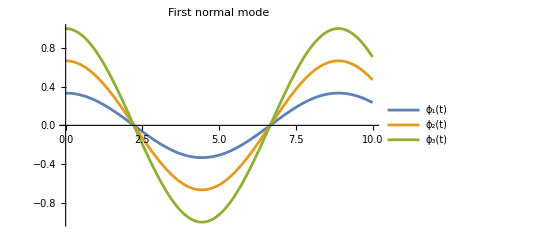

```mathematica
Plot[Evaluate@(Subscript[ϕ, 1][t, A, δ ] /. {g -> 1, l -> 1, A -> 1, δ-> 0} ), {t, 0, tMax}, PlotLegends->legendToPlot, PlotLabel->"First normal mode"]
```

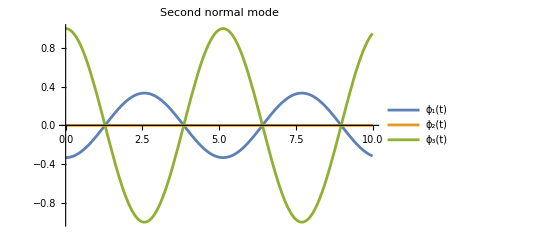

```mathematica
Subscript[ϕ, 2][t_, A_, δ_] = A a2 Cos[Subscript[ω, 2] t - δ];
Plot[Evaluate@(Subscript[ϕ, 2][t, A, δ ] /. {g -> 1, l -> 1, A -> 1, δ-> 0} ), {t, 0, tMax}, PlotLegends->legendToPlot, PlotLabel->"Second normal mode"]
```

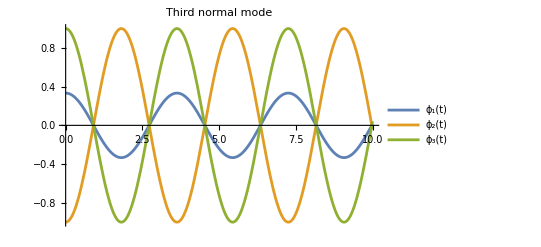

```mathematica
Subscript[ϕ, 3][t_, A_, δ_] = A a3 Cos[Subscript[ω, 3] t - δ];
Plot[Evaluate@(Subscript[ϕ, 3][t, A, δ ] /. {g -> 1, l -> 1, A -> 1, δ-> 0} ), {t, 0, tMax}, PlotLegends->legendToPlot, PlotLabel->"Third normal mode"]
```

## Lagrange’s equations

```mathematica
Lf[t_] = L /. {Subscript[ϕ̇, 1]-> Subscript[ϕ, 1]'[t], Subscript[ϕ̇, 2]-> Subscript[ϕ, 2]'[t], Subscript[ϕ̇, 3]-> Subscript[ϕ, 3]'[t], Subscript[ϕ, 1]-> Subscript[ϕ, 1][t], Subscript[ϕ, 2]-> Subscript[ϕ, 2][t], Subscript[ϕ, 3]-> Subscript[ϕ, 3][t]};
```

```mathematica
lhs1 = D[D[Lf[t], Subscript[ϕ, 1]'[t]], t];
lhs1 // Simplify
```

l^2 m (-3 Sin[ϕ_1[t]-ϕ_2[t]] (ϕ_1'[t]-ϕ_2'[t]) ϕ_2'[t]-Sin[ϕ_1[t]-ϕ_3[t]] (ϕ_1'[t]-ϕ_3'[t]) ϕ_3'[t]+9 ϕ_1''[t]+3 Cos[ϕ_1[t]-ϕ_2[t]] ϕ_2''[t]+Cos[ϕ_1[t]-ϕ_3[t]] ϕ_3''[t])

```mathematica
rhs1 = D[Lf[t], Subscript[ϕ, 1][t]];
```

```mathematica
lhs2 = D[D[Lf[t], Subscript[ϕ, 2]'[t]], t];
lhs2 // Simplify
```

1/2 l^2 m (-6 Sin[ϕ_1[t]-ϕ_2[t]] ϕ_1'[t] (ϕ_1'[t]-ϕ_2'[t])-2 Sin[ϕ_2[t]-ϕ_3[t]] (ϕ_2'[t]-ϕ_3'[t]) ϕ_3'[t]+6 Cos[ϕ_1[t]-ϕ_2[t]] ϕ_1''[t]+6 ϕ_2''[t]+2 Cos[ϕ_2[t]-ϕ_3[t]] ϕ_3''[t])

```mathematica
rhs2 = D[Lf[t], Subscript[ϕ, 2][t]]
```

-3 g l m Sin[ϕ_2[t]]+1/2 l^2 m (6 Sin[ϕ_1[t]-ϕ_2[t]] ϕ_1'[t] ϕ_2'[t]-2 Sin[ϕ_2[t]-ϕ_3[t]] ϕ_2'[t] ϕ_3'[t])

```mathematica
lhs3 = D[D[Lf[t], Subscript[ϕ, 3]'[t]], t];
lhs3 // Simplify
```

l^2 m (-Sin[ϕ_1[t]-ϕ_3[t]] ϕ_1'[t] (ϕ_1'[t]-ϕ_3'[t])-Sin[ϕ_2[t]-ϕ_3[t]] ϕ_2'[t] (ϕ_2'[t]-ϕ_3'[t])+Cos[ϕ_1[t]-ϕ_3[t]] ϕ_1''[t]+Cos[ϕ_2[t]-ϕ_3[t]] ϕ_2''[t]+ϕ_3''[t])

```mathematica
rhs3 = D[Lf[t], Subscript[ϕ, 3][t]]
```

-g l m Sin[ϕ_3[t]]+1/2 l^2 m (2 Sin[ϕ_1[t]-ϕ_3[t]] ϕ_1'[t] ϕ_3'[t]+2 Sin[ϕ_2[t]-ϕ_3[t]] ϕ_2'[t] ϕ_3'[t])

```mathematica
subs = { l-> 1, g->1, m->1};
eq1 = (lhs1  == rhs1) /. subs ;
eq2 = (lhs2  == rhs2) /. subs ;
eq3 = (lhs3  == rhs3) /. subs ;
tMax = 10;
```

```mathematica
sl1 = NDSolve[{eq1, eq2, eq3,  Subscript[ϕ, 1][0] == 0.1, Subscript[ϕ, 2][0] == 0.2, Subscript[ϕ, 3][0] == 0.3, Subscript[ϕ, 1]'[0] == Subscript[ϕ, 2]'[0] == Subscript[ϕ, 3]'[0] == 0}, {Subscript[ϕ, 1], Subscript[ϕ, 2], Subscript[ϕ, 3]}, {t, 0, tMax}];
```

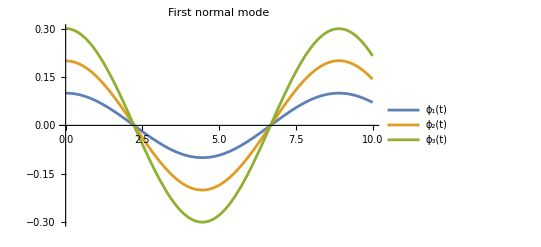

```mathematica
Plot[Evaluate[{Subscript[ϕ, 1][t], Subscript[ϕ, 2][t], Subscript[ϕ, 3][t]} /. sl1], {t, 0, tMax},PlotLegends->legendToPlot, PlotLabel->"First normal mode"]
```

```mathematica
sl2 = NDSolve[{eq1, eq2, eq3,  Subscript[ϕ, 1][0] == -0.1, Subscript[ϕ, 2][0] == 0, Subscript[ϕ, 3][0] == 0.3, Subscript[ϕ, 1]'[0] == Subscript[ϕ, 2]'[0] == Subscript[ϕ, 3]'[0] == 0}, {Subscript[ϕ, 1], Subscript[ϕ, 2], Subscript[ϕ, 3]}, {t, 0, tMax}];
```

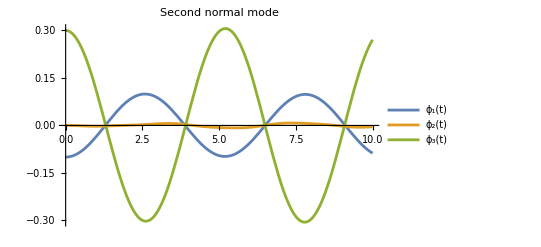

```mathematica
Plot[Evaluate[{Subscript[ϕ, 1][t], Subscript[ϕ, 2][t], Subscript[ϕ, 3][t]} /. sl2], {t, 0, tMax},PlotLegends->legendToPlot, PlotLabel->"Second normal mode"]
```

```mathematica
sl3 = NDSolve[{eq1, eq2, eq3,  Subscript[ϕ, 1][0] == 0.1, Subscript[ϕ, 2][0] == -0.3, Subscript[ϕ, 3][0] == 0.3, Subscript[ϕ, 1]'[0] == Subscript[ϕ, 2]'[0] == Subscript[ϕ, 3]'[0] == 0}, {Subscript[ϕ, 1], Subscript[ϕ, 2], Subscript[ϕ, 3]}, {t, 0, tMax}];
```

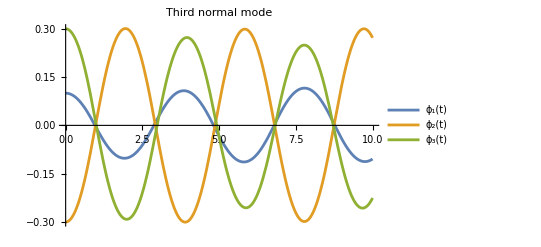

```mathematica
Plot[Evaluate[{Subscript[ϕ, 1][t], Subscript[ϕ, 2][t], Subscript[ϕ, 3][t]} /. sl3], {t, 0, tMax},PlotLegends->legendToPlot, PlotLabel->"Third normal mode"]
```

```mathematica
tMaxAnim = 15;
sl = NDSolve[{eq1, eq2, eq3,  Subscript[ϕ, 1][0] == -0.15, Subscript[ϕ, 2][0] == -0.35, Subscript[ϕ, 3][0] == 0.25, Subscript[ϕ, 1]'[0] == Subscript[ϕ, 2]'[0] == Subscript[ϕ, 3]'[0] == 0}, {Subscript[ϕ, 1], Subscript[ϕ, 2], Subscript[ϕ, 3]}, {t, 0, tMaxAnim}];
```

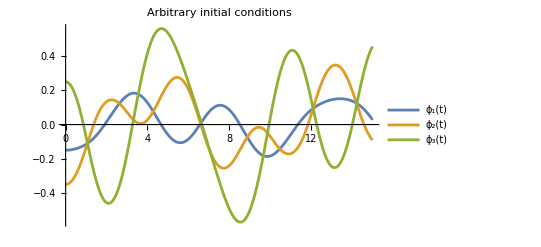

```mathematica
Plot[Evaluate[{Subscript[ϕ, 1][t], Subscript[ϕ, 2][t], Subscript[ϕ, 3][t]} /. sl], {t, 0, tMaxAnim},PlotLegends->legendToPlot, PlotLabel->"Arbitrary initial conditions"]
```

## Animation

```mathematica
x1[ϕ1_, ϕ2_, ϕ3_] =  Sin[ϕ1];
y1 [ϕ1_, ϕ2_, ϕ3_] = - Cos[ϕ1];
x2[ϕ1_, ϕ2_, ϕ3_] = Sin[ϕ1] + Sin[ϕ2];
y2 [ϕ1_, ϕ2_, ϕ3_] = - Cos[ϕ1] - Cos[ϕ2];
x3[ϕ1_, ϕ2_, ϕ3_] =  Sin[ϕ1 ]+  Sin[ϕ2] +  Sin[ϕ3];y3 [ϕ1_, ϕ2_, ϕ3_] = - Cos[ϕ1] - Cos[ϕ2] - Cos[ϕ3];
```

```mathematica
Manipulate[
Module[
{phiValues,x1Val,y1Val,x2Val,y2Val,x3Val,y3Val},(*Precompute values to avoid repeated calculations*)phiValues={Subscript[ϕ,1][t],Subscript[ϕ,2][t],Subscript[ϕ,3][t]}/. sl;
x1Val=x1@@phiValues[[1]];
y1Val=y1@@phiValues[[1]];
x2Val=x2@@phiValues[[1]];
y2Val=y2@@phiValues[[1]];
x3Val=x3@@phiValues[[1]];
y3Val=y3@@phiValues[[1]];
Show[
Graphics[{
Orange,
Disk[{x3Val,y3Val},0.01],
Disk[{x2Val,y2Val},0.02],
Disk[{x1Val,y1Val},0.06],
Black, 
Line[{{x3Val,y3Val},{x2Val,y2Val}}],
Line[{{x2Val,y2Val},{x1Val,y1Val}}],
Line[{{x1Val,y1Val},{0,0}}],
Disk[{0, 0}, 0.02]
}],
AxesLabel->{"x","y"},
Axes->True,
PlotRange->{{-1,1},{0,-3}}
]
],
{t,0,tMaxAnim}
]
```

```mathematica
frames=Table[Module[
{phiValues,x1Val,y1Val,x2Val,y2Val,x3Val,y3Val},(*Precompute values to avoid repeated calculations*)phiValues={Subscript[ϕ,1][t],Subscript[ϕ,2][t],Subscript[ϕ,3][t]}/. sl;
x1Val=x1@@phiValues[[1]];
y1Val=y1@@phiValues[[1]];
x2Val=x2@@phiValues[[1]];
y2Val=y2@@phiValues[[1]];
x3Val=x3@@phiValues[[1]];
y3Val=y3@@phiValues[[1]];
Show[
Graphics[{
Orange,
Disk[{x3Val,y3Val},0.01],
Disk[{x2Val,y2Val},0.02],
Disk[{x1Val,y1Val},0.06],
Black, 
Line[{{x3Val,y3Val},{x2Val,y2Val}}],
Line[{{x2Val,y2Val},{x1Val,y1Val}}],
Line[{{x1Val,y1Val},{0,0}}],
Disk[{0, 0}, 0.02]
}],
AxesLabel->{"x","y"},
Axes->True,
PlotRange->{{-1,1},{0,-3}}
]
],
{t,0,tMaxAnim,0.035} (*Adjust step size to control frame rate*)];

Export["animation.mp4",frames,"FrameRate"->30]
```

animation.mp4